# International Interaction Game

## Quantum-like Signorino’s Backward Induction Model

Quantum Extension of Signorino’s International Interaction Game Model

### Quantum-like Backward Induction Functions

```mathematica
(*Quantum Extension of Signorino's International Interaction Game Model Based on the classical implementation in signorino_model.m*)(*Quantum Backward Induction Functions*)q10quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq10quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

q11quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq11quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p8quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp8quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p12quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp12quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

q9quantum[theta1_,theta2_,U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*U2War2+notp12val*U2Cap1;
numerator=Exp[l2*UP2N12];
denominator=Exp[l2*UP2N12]+Exp[l2*U2Nego];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq9quantum[theta1_,theta2_,U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*U2War2+notp12val*U2Cap1;
numerator=Exp[l2*UP2N12];
denominator=Exp[l2*UP2N12]+Exp[l2*U2Nego];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p7quantum[theta1_,theta2_,U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
numerator=Exp[l1*UP1N11];
denominator=Exp[l1*UP1N11]+Exp[l1*U1Nego];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp7quantum[theta1_,theta2_,U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
numerator=Exp[l1*UP1N11];
denominator=Exp[l1*UP1N11]+Exp[l1*U1Nego];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

q6quantum[theta1_,theta2_,U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p8val,notp8val,UP2N8,q11val,notq11val,U2N11,UP2N7,numerator,denominator,exponentialFactor},p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*U2War2+notp8val*U2Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
U2N11=q11val*U2War1+notq11val*U2Cap2;
UP2N7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2]*U2N11+notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2]*U2Nego;
numerator=Exp[l2*UP2N8];
denominator=Exp[l2*UP2N8]+Exp[l2*UP2N7];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq6quantum[theta1_,theta2_,U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p8val,notp8val,UP2N8,q11val,notq11val,U2N11,UP2N7,numerator,denominator,exponentialFactor},p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*U2War2+notp8val*U2Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
U2N11=q11val*U2War1+notq11val*U2Cap2;
UP2N7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2]*U2N11+notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2]*U2Nego;
numerator=Exp[l2*UP2N8];
denominator=Exp[l2*UP2N8]+Exp[l2*UP2N7];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p5quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q10val,notq10val,UP1N10,q9val,notq9val,UP1N9,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*U1War2+notp12val*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*U1War1+notq10val*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*UP1N12+notq9val*U1Nego;
numerator=Exp[l1*UP1N10];
denominator=Exp[l1*UP1N10]+Exp[l1*UP1N9];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp5quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q10val,notq10val,UP1N10,q9val,notq9val,UP1N9,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*U1War2+notp12val*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*U1War1+notq10val*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*UP1N12+notq9val*U1Nego;
numerator=Exp[l1*UP1N10];
denominator=Exp[l1*UP1N10]+Exp[l1*UP1N9];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p4quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,p8val,notp8val,UP1N8,p7val,notp7val,UP1N7,q6val,notq6val,UP1N6,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*U1War2+notp8val*U1Cap1;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*UP1N11+notp7val*U1Nego;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*UP1N8+notq6val*UP1N7;
numerator=Exp[l1*UP1N6];
denominator=Exp[l1*UP1N6]+Exp[l1*U1Acq1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp4quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,p8val,notp8val,UP1N8,p7val,notp7val,UP1N7,q6val,notq6val,UP1N6,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*U1War2+notp8val*U1Cap1;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*UP1N11+notp7val*U1Nego;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*UP1N8+notq6val*UP1N7;
numerator=Exp[l1*UP1N6];
denominator=Exp[l1*UP1N6]+Exp[l1*U1Acq1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

q3quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,q10val,notq10val,UP2N10,q9val,notq9val,UP2N9,p5val,notp5val,UP2N5,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*U2War2+notp12val*U2Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N10=q10val*U2War1+notq10val*U2Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP2N9=q9val*UP2N12+notq9val*U2Nego;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP2N5=p5val*UP2N10+notp5val*UP2N9;
numerator=Exp[l2*UP2N5];
denominator=Exp[l2*UP2N5]+Exp[l2*U2Acq2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq3quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,q10val,notq10val,UP2N10,q9val,notq9val,UP2N9,p5val,notp5val,UP2N5,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*U2War2+notp12val*U2Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N10=q10val*U2War1+notq10val*U2Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP2N9=q9val*UP2N12+notq9val*U2Nego;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP2N5=p5val*UP2N10+notp5val*UP2N9;
numerator=Exp[l2*UP2N5];
denominator=Exp[l2*UP2N5]+Exp[l2*U2Acq2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

q2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP2N11,p7val,notp7val,UP2N7,p8val,notp8val,UP2N8,q6val,notq6val,UP2N6,p4val,notp4val,UP2N4,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N11=q11val*U2War1+notq11val*U2Cap2;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP2N7=p7val*UP2N11+notp7val*U2Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*U2War2+notp8val*U2Cap1;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP2N6=q6val*UP2N8+notq6val*UP2N7;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP2N4=p4val*UP2N6+notp4val*U2Acq1;
numerator=Exp[l2*UP2N4];
denominator=Exp[l2*UP2N4]+Exp[l2*U2SQ];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP2N11,p7val,notp7val,UP2N7,p8val,notp8val,UP2N8,q6val,notq6val,UP2N6,p4val,notp4val,UP2N4,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N11=q11val*U2War1+notq11val*U2Cap2;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP2N7=p7val*UP2N11+notp7val*U2Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*U2War2+notp8val*U2Cap1;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP2N6=q6val*UP2N8+notq6val*UP2N7;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP2N4=p4val*UP2N6+notp4val*U2Acq1;
numerator=Exp[l2*UP2N4];
denominator=Exp[l2*UP2N4]+Exp[l2*U2SQ];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q11val,notq11val,UP1N11,q9val,notq9val,UP1N9,p7val,notp7val,UP1N7,p8val,notp8val,UP1N8,q10val,notq10val,UP1N10,q6val,notq6val,UP1N6,p5val,notp5val,UP1N5,p4val,notp4val,UP1N4,q3val,notq3val,UP1N3,q2val,notq2val,UP1N2,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*U1War1+notp12val*U1Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*UP1N12+notq9val*U1Nego;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*UP1N11+notp7val*U1Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*U1War2+notp8val*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*U1War1+notq10val*U1Cap2;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*UP1N8+notq6val*UP1N7;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP1N5=p5val*UP1N10+notp5val*UP1N9;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP1N4=p4val*UP1N6+notp4val*U1Acq1;
q3val=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notq3val=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
UP1N3=q3val*UP1N5+notq3val*U1Acq2;
q2val=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notq2val=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
UP1N2=q2val*UP1N4+notq2val*U1SQ;
numerator=Exp[l1*UP1N3];
denominator=Exp[l1*UP1N3]+Exp[l1*UP1N2];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q11val,notq11val,UP1N11,q9val,notq9val,UP1N9,p7val,notp7val,UP1N7,p8val,notp8val,UP1N8,q10val,notq10val,UP1N10,q6val,notq6val,UP1N6,p5val,notp5val,UP1N5,p4val,notp4val,UP1N4,q3val,notq3val,UP1N3,q2val,notq2val,UP1N2,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*U1War1+notp12val*U1Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*UP1N12+notq9val*U1Nego;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*UP1N11+notp7val*U1Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*U1War2+notp8val*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*U1War1+notq10val*U1Cap2;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*UP1N8+notq6val*UP1N7;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP1N5=p5val*UP1N10+notp5val*UP1N9;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP1N4=p4val*UP1N6+notp4val*U1Acq1;
q3val=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notq3val=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
UP1N3=q3val*UP1N5+notq3val*U1Acq2;
q2val=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notq2val=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
UP1N2=q2val*UP1N4+notq2val*U1SQ;
numerator=Exp[l1*UP1N3];
denominator=Exp[l1*UP1N3]+Exp[l1*UP1N2];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]
```

### Outcome Functions

```mathematica
SQquantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,notq2},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notq2=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notp1*notq2]

ACQ1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,notp4},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notp4=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp1*q2*notp4]

ACQ2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p1,notq3},p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notq3=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
p1*notq3]

NEGOquantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p1,notp1,q2,q3,p4,notp5,notq6,notp7,notq9},p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notp7=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notq9=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notp1*q2*p4*notq6*notp7+p1*q3*notp5*notq9]

CAP1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,p4,q6,notp8,p1,q3,notp5,q9,notp12},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
q6=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notp8=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
q9=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notp12=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp1*q2*p4*q6*notp8+p1*q3*notp5*q9*notp12]

CAP2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,p4,notq6,p7,notq11,p1,q3,p5,notq10},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
p7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notq11=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
p5=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notq10=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notp1*q2*p4*notq6*p7*notq11+p1*q3*p5*notq10]

WAR1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,p1,q2,p4,notq6,p7,q11,q3,q10,p5},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
p7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
q11=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
q10=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
p5=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp1*q2*p4*notq6*p7*q11+p1*q3*p5*q10]

WAR2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,p1,q2,p4,q6,p8,q3,notp5,q9,p12},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
q6=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
p8=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
q9=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
p12=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp1*q2*p4*q6*p8+p1*q3*notp5*q9*p12]
```

### Quantum State Processing Functions

```mathematica
normalizeQuantumState[amplitudes_List]:=Module[{sumSquaredMagnitudes},sumSquaredMagnitudes=Total[Abs[#]^2&/@amplitudes];
If[sumSquaredMagnitudes==0,amplitudes,#/Sqrt[sumSquaredMagnitudes]&/@amplitudes]]

createSuperpositionState[normalizedAmplitudes_List]:=Module[{basisStates,superposition},(*Create column vectors for each basis state*)basisStates={{1,0,0,0,0,0,0,0},(*SQ*){0,1,0,0,0,0,0,0},(*ACQ1*){0,0,1,0,0,0,0,0},(*ACQ2*){0,0,0,1,0,0,0,0},(*NEGO*){0,0,0,0,1,0,0,0},(*CAP1*){0,0,0,0,0,1,0,0},(*CAP2*){0,0,0,0,0,0,1,0},(*WAR1*){0,0,0,0,0,0,0,1}  (*WAR2*)};
superposition=Total[MapThread[Times,{normalizedAmplitudes,basisStates}]];
superposition]

computeOutcomeProbabilities[superpositionState_]:=Module[{projectionOps,probabilities},projectionOps=Table[projectionOperator[i],{i,0,7}];
probabilities=Table[Module[{prob},prob=Re[Conjugate[superpositionState].projectionOps[[i+1]].superpositionState];
If[NumericQ[prob],prob,Abs[superpositionState[[i+1]]]^2]],{i,0,7}];
probabilities]
```

### Aux Functions

#### projectionOperator

```mathematica
projectionOperator[index_Integer]:=Module[{mat},mat=ConstantArray[0,{8,8}];
If[0<=index<=7,mat[[index+1,index+1]]=1];
mat]
```

#### getOutcome

```mathematica
getOutcome[index_Integer]:=Switch[index,0,"SQ",1,"ACQ1",2,"ACQ2",3,"NEGO",4,"CAP1",5,"CAP2",6,"WAR1",7,"WAR2",_,"Invalid"]
```

#### getIndexFromOutcome

```mathematica
getIndexFromOutcome[outcome_String]:=Switch[outcome,"SQ",0,"ACQ1",1,"ACQ2",2,"NEGO",3,"CAP1",4,"CAP2",5,"WAR1",6,"WAR2",7,_,"Invalid"]
```

#### calculateQuantumOutcome

```mathematica
calculateQuantumOutcome[data_,rowIndex_Integer,theta1_:0,theta2_:0,l1_:1,l2_:1]:=Module[{utils,quantumAmplitudes,normalizedAmplitudes,finalProbabilities,outcomes,maxIndex,prediction},utils=extractUtilities[data,rowIndex];
If[utils===$Failed,Return[$Failed]];
(*Compute quantum probability amplitudes*)quantumAmplitudes=Quiet[{SQquantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],ACQ1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],ACQ2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],NEGOquantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],CAP1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],CAP2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],WAR1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],WAR2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2]}];
(*Calculate final probabilities directly from amplitudes*)finalProbabilities=Abs[#]^2&/@quantumAmplitudes;
(*Normalize probabilities*)finalProbabilities=finalProbabilities/Total[finalProbabilities];
outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1","WAR2"};
maxIndex=Position[finalProbabilities,Max[finalProbabilities]][[1,1]];
prediction=outcomes[[maxIndex]];
Association["SQ"->finalProbabilities[[1]],"ACQ1"->finalProbabilities[[2]],"ACQ2"->finalProbabilities[[3]],"NEGO"->finalProbabilities[[4]],"CAP1"->finalProbabilities[[5]],"CAP2"->finalProbabilities[[6]],"WAR1"->finalProbabilities[[7]],"WAR2"->finalProbabilities[[8]],"prediction"->prediction,"groundtruth"->utils["groundtruth"],"utilities"->utils,"theta1"->theta1,"theta2"->theta2,"l1"->l1,"l2"->l2,"total"->Total[finalProbabilities]]]
```

#### processQuantumDataset

```mathematica
(*Process Quantum Dataset*)
processQuantumDataset[data_,theta1_:0,theta2_:0,l1_:1,l2_:1]:=Module[{results,i},If[data===$Failed,Print["Error: Invalid data passed to processQuantumDataset"];
Return[{}]];
Print["Processing ",data["nrows"]," rows with quantum model..."];
Print["Parameters: θ1=",theta1,", θ2=",theta2,", λ1=",l1,", λ2=",l2];
results={};
Do[Module[{result},If[Mod[i,50]==0,Print["Processing row ",i,"/",data["nrows"]]];
result=calculateQuantumOutcome[data,i,theta1,theta2,l1,l2];
If[result=!=$Failed,AppendTo[results,result],Print["Warning: Failed to process row ",i]]],{i,1,data["nrows"]}];
Print["Successfully processed ",Length[results]," out of ",data["nrows"]," rows"];
results]
```

#### getQuantumPredictions

```mathematica
getQuantumPredictions[data_,theta1_:0,theta2_:0,l1_:1,l2_:1]:=Module[{results,predictions,groundTruth,validResults,cleanPredictions,cleanGroundTruth,validIndices},Print["Computing quantum predictions for dataset..."];
results=processQuantumDataset[data,theta1,theta2,l1,l2];
If[Length[results]==0,Print["Error: No valid results computed"];Return[$Failed]];
validResults=Select[results,#=!=$Failed&];
predictions=Table[validResults[[i]]["prediction"],{i,Length[validResults]}];
groundTruth=Table[validResults[[i]]["groundtruth"],{i,Length[validResults]}];
validIndices=Position[predictions,Except["ERROR"]]//Flatten;
cleanPredictions=predictions[[validIndices]];
cleanGroundTruth=groundTruth[[validIndices]];
Print["Valid predictions: ",Length[cleanPredictions]," out of ",Length[predictions]];
Association["predictions"->cleanPredictions,"groundtruth"->cleanGroundTruth,"results"->validResults,"accuracy"->If[Length[cleanPredictions]>0,N[Count[MapThread[Equal,{cleanPredictions,cleanGroundTruth}],True]/Length[cleanPredictions]],0]]]
```

#### calculateQuantumAccuracy

```mathematica
calculateQuantumAccuracy[results_]:=Module[{predTruth,correct},If[Length[results]==0,Print["Warning: No results to calculate accuracy from"];
Return[0]];
predTruth=extractPredictionsAndGroundtruth[results];
If[Length[predTruth["predictions"]]==0,Print["Warning: No valid predictions found"];
Return[0]];
correct=MapThread[Equal,{predTruth["predictions"],predTruth["groundtruth"]}];
N[Count[correct,True]/Length[correct]]]
```

#### plotQuantumConfusionMatrix

```mathematica
plotQuantumConfusionMatrix[results_,theta1_:0,theta2_:0,l1_:1,l2_:1,title_:"Quantum Confusion Matrix"]:=Module[{predictions,groundTruths,outcomes,confusionData,accuracy,predTruth},If[Length[results]==0,Print["Warning: No results provided for confusion matrix"];
Return[Null]];
predTruth=extractPredictionsAndGroundtruth[results];
predictions=predTruth["predictions"];
groundTruths=predTruth["groundtruth"];
If[Length[predictions]==0,Print["Warning: No valid predictions found"];
Return[Null]];
accuracy=N[Count[MapThread[Equal,{predictions,groundTruths}],True]/Length[results]];
outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1"};
confusionData=Table[Count[MapThread[List,{groundTruths,predictions}],{actualOutcome,predictedOutcome}],{actualOutcome,outcomes},{predictedOutcome,outcomes}];
Print[Style[title,16,Bold]];
Print[Style["θ1 = "<>ToString[theta1]<>" θ2 = "<>ToString[theta2]<>" λ1 = "<>ToString[l1]<>" λ2 = "<>ToString[l2]<>" | Accuracy = "<>ToString[N[accuracy]],14]];
Print[""];
Grid[Prepend[MapThread[Prepend,{confusionData,outcomes}],Prepend[outcomes,Style["Actual \\ Predicted",Bold]]],Frame->All,Alignment->Center,Background->{None,{LightBlue,None}},ItemStyle->{Automatic,{Bold,Automatic}},Spacings->{2,1},FrameStyle->Thick,Dividers->{{2->Thick},{2->Thick}}]]
```

#### loadData

```mathematica
loadData[filename_String]:=Module[{rawData,headers,dataRows,groundtruth,utilityData,cleanedData,requiredColumns,missingColumns},

Print["Loading CSV file: ",filename];
rawData=Import[filename,"CSV"];

If[Head[rawData]=!=List||Length[rawData]<2,
Print["Error: Could not load CSV file or file is empty"];
Return[$Failed]
];

headers=First[rawData];
dataRows=Rest[rawData];

Print["Loaded ",Length[dataRows]," rows with ",Length[headers]," columns"];
cleanedData=Map[Function[row,Map[Function[cell,If[NumericQ[cell],cell,If[StringQ[cell]&&StringMatchQ[cell,NumberString],ToExpression[cell],cell]]],row]],dataRows];
groundtruth=cleanedData[[All,-1]];

utilityData=Association[Table[headers[[i]]->cleanedData[[All,i]],{i,Length[headers]}]];

requiredColumns={"wrTu1wr2","wrTu1cp1","wrTu1cp2","wrTu1wr1","wrTu1neg","wrTu1ac1","wrTu1ac2","wrTu1sq","wrTu2wr2","wrTu2cp1","wrTu2wr1","wrTu2cp2","wrTu2neg","wrTu2ac1","wrTu2ac2","wrTu2sq"};
missingColumns=Select[requiredColumns,!KeyExistsQ[utilityData,#]&];

If[Length[missingColumns]>0,
Print["Warning: Missing required columns: ",missingColumns];
];

Association[
"groundtruth"->groundtruth,
"data"->utilityData,
"nrows"->Length[cleanedData],
"headers"->headers,
"filename"->filename]
]
```

#### extractUtilities

```mathematica
extractUtilities[data_,rowIndex_Integer]:=Module[{row,utils},
If[rowIndex<1||rowIndex>data["nrows"],
Print["Error: Row index ",rowIndex," out of range [1, ",data["nrows"],"]"];
Return[$Failed]
];

row=data["data"];
utils=Association[];

(*Player 1 utilities*)
utils["U1War2"]=If[KeyExistsQ[row,"wrTu1wr2"]&&NumericQ[row["wrTu1wr2"][[rowIndex]]],row["wrTu1wr2"][[rowIndex]],0.0];
utils["U1Cap1"]=If[KeyExistsQ[row,"wrTu1cp1"]&&NumericQ[row["wrTu1cp1"][[rowIndex]]],row["wrTu1cp1"][[rowIndex]],0.0];
utils["U1Cap2"]=If[KeyExistsQ[row,"wrTu1cp2"]&&NumericQ[row["wrTu1cp2"][[rowIndex]]],row["wrTu1cp2"][[rowIndex]],0.0];
utils["U1War1"]=If[KeyExistsQ[row,"wrTu1wr1"]&&NumericQ[row["wrTu1wr1"][[rowIndex]]],row["wrTu1wr1"][[rowIndex]],0.0];
utils["U1Nego"]=If[KeyExistsQ[row,"wrTu1neg"]&&NumericQ[row["wrTu1neg"][[rowIndex]]],row["wrTu1neg"][[rowIndex]],0.0];
utils["U1Acq1"]=If[KeyExistsQ[row,"wrTu1ac1"]&&NumericQ[row["wrTu1ac1"][[rowIndex]]],row["wrTu1ac1"][[rowIndex]],0.0];
utils["U1Acq2"]=If[KeyExistsQ[row,"wrTu1ac2"]&&NumericQ[row["wrTu1ac2"][[rowIndex]]],row["wrTu1ac2"][[rowIndex]],0.0];
utils["U1SQ"]=If[KeyExistsQ[row,"wrTu1sq"]&&NumericQ[row["wrTu1sq"][[rowIndex]]],row["wrTu1sq"][[rowIndex]],0.0];

(*Player 2 utilities*)
utils["U2War2"]=If[KeyExistsQ[row,"wrTu2wr2"]&&NumericQ[row["wrTu2wr2"][[rowIndex]]],row["wrTu2wr2"][[rowIndex]],0.0];
utils["U2Cap1"]=If[KeyExistsQ[row,"wrTu2cp1"]&&NumericQ[row["wrTu2cp1"][[rowIndex]]],row["wrTu2cp1"][[rowIndex]],0.0];
utils["U2War1"]=If[KeyExistsQ[row,"wrTu2wr1"]&&NumericQ[row["wrTu2wr1"][[rowIndex]]],row["wrTu2wr1"][[rowIndex]],0.0];
utils["U2Cap2"]=If[KeyExistsQ[row,"wrTu2cp2"]&&NumericQ[row["wrTu2cp2"][[rowIndex]]],row["wrTu2cp2"][[rowIndex]],0.0];
utils["U2Nego"]=If[KeyExistsQ[row,"wrTu2neg"]&&NumericQ[row["wrTu2neg"][[rowIndex]]],row["wrTu2neg"][[rowIndex]],0.0];
utils["U2Acq1"]=If[KeyExistsQ[row,"wrTu2ac1"]&&NumericQ[row["wrTu2ac1"][[rowIndex]]],row["wrTu2ac1"][[rowIndex]],0.0];
utils["U2Acq2"]=If[KeyExistsQ[row,"wrTu2ac2"]&&NumericQ[row["wrTu2ac2"][[rowIndex]]],row["wrTu2ac2"][[rowIndex]],0.0];
utils["U2SQ"]=If[KeyExistsQ[row,"wrTu2sq"]&&NumericQ[row["wrTu2sq"][[rowIndex]]],row["wrTu2sq"][[rowIndex]],0.0];
utils["Agent1"]=If[KeyExistsQ[row,"ISOShNm1"],row["ISOShNm1"][[rowIndex]],"Unknown"];
utils["Agent2"]=If[KeyExistsQ[row,"ISOShNm2"],row["ISOShNm2"][[rowIndex]],"Unknown"];

(*Additional information*)
utils["groundtruth"]=data["groundtruth"][[rowIndex]];
utils["ccode1"]=If[KeyExistsQ[row,"ccode1"]&&NumericQ[row["ccode1"][[rowIndex]]],row["ccode1"][[rowIndex]],0];
utils["ccode2"]=If[KeyExistsQ[row,"ccode2"]&&NumericQ[row["ccode2"][[rowIndex]]],row["ccode2"][[rowIndex]],0];
utils["year"]=If[KeyExistsQ[row,"year"]&&NumericQ[row["year"][[rowIndex]]],row["year"][[rowIndex]],0];
utils]
```

#### extractPredictionsAndGroundtruth

```mathematica
extractPredictionsAndGroundtruth[results_]:=Module[{predictions,groundTruth,outcomes},
outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1"};
predictions=
Table[
Module[{outcomeProbs,maxVal,maxOutcome},
outcomeProbs=
Association[
"ACQ1"->If[KeyExistsQ[results[[i]],"ACQ1"]&&NumericQ[results[[i]]["ACQ1"]],results[[i]]["ACQ1"],0],
"ACQ2"->If[KeyExistsQ[results[[i]],"ACQ2"]&&NumericQ[results[[i]]["ACQ2"]],results[[i]]["ACQ2"],0],
"CAP1"->If[KeyExistsQ[results[[i]],"CAP1"]&&NumericQ[results[[i]]["CAP1"]],results[[i]]["CAP1"],0],
"CAP2"->If[KeyExistsQ[results[[i]],"CAP2"]&&NumericQ[results[[i]]["CAP2"]],results[[i]]["CAP2"],0],
"NEGO"->If[KeyExistsQ[results[[i]],"NEGO"]&&NumericQ[results[[i]]["NEGO"]],results[[i]]["NEGO"],0],
"SQ"->If[KeyExistsQ[results[[i]],"SQ"]&&NumericQ[results[[i]]["SQ"]],results[[i]]["SQ"],0],
"WAR1"->If[KeyExistsQ[results[[i]],"WAR1"]&&NumericQ[results[[i]]["WAR1"]],results[[i]]["WAR1"],0]
];

(*Find outcome with maximum probability*)
maxVal=Max[Values[outcomeProbs]];
maxOutcome=First[Keys[Select[outcomeProbs,#==maxVal&]]];
maxOutcome],{i,Length[results]}];

groundTruth=Table[If[KeyExistsQ[results[[i]],"groundtruth"],results[[i]]["groundtruth"],"UNKNOWN"],{i,Length[results]}];
Association[
"predictions"->predictions,
"groundtruth"->groundTruth]]
```

### Optimization Functions

```mathematica
(*Grid Search Function for Optimal Theta Parameters*)
gridSearchQuantumThetas[data_,theta1Range_List,theta2Range_List,l1_:1,l2_:1,verbose_:True]:=Module[{results,bestAccuracy,bestTheta1,bestTheta2,totalCombinations,currentCombination,startTime,gridResults,theta1Values,theta2Values},(*Input validation*)If[data===$Failed||!KeyExistsQ[data,"nrows"],Print["Error: Invalid data provided"];
Return[$Failed]];
(*Extract theta values from ranges*)theta1Values=theta1Range;
theta2Values=theta2Range;
totalCombinations=Length[theta1Values]*Length[theta2Values];
currentCombination=0;
bestAccuracy=0;
bestTheta1=First[theta1Values];
bestTheta2=First[theta2Values];
If[verbose,Print["Starting grid search over ",totalCombinations," parameter combinations..."];
Print["Theta1 range: ",theta1Values];
Print["Theta2 range: ",theta2Values];
Print["Lambda1 = ",l1,", Lambda2 = ",l2];
Print["Dataset size: ",data["nrows"]," rows"];
Print[""];];
startTime=AbsoluteTime[];
gridResults={};
(*Grid search loop*)Do[Module[{currentResults,currentAccuracy,elapsedTime,estimatedTotal,estimatedRemaining},currentCombination++;
If[verbose&&Mod[currentCombination,Max[1,Floor[totalCombinations/20]]]==0,elapsedTime=AbsoluteTime[]-startTime;
estimatedTotal=elapsedTime*totalCombinations/currentCombination;
estimatedRemaining=estimatedTotal-elapsedTime;
Print["Progress: ",currentCombination,"/",totalCombinations," (",N[100*currentCombination/totalCombinations,3],"%)"];
Print["Elapsed: ",N[elapsedTime/60,2]," min, Estimated remaining: ",N[estimatedRemaining/60,2]," min"];
Print["Current best: θ1=",bestTheta1,", θ2=",bestTheta2,", Accuracy=",N[bestAccuracy,4]];
Print[""];];
(*Calculate results for current theta combination*)currentResults=Quiet[processQuantumDataset[data,theta1,theta2,l1,l2]];
If[Length[currentResults]>0,currentAccuracy=calculateQuantumAccuracy[currentResults];
(*Store result*)AppendTo[gridResults,Association["theta1"->theta1,"theta2"->theta2,"accuracy"->currentAccuracy,"l1"->l1,"l2"->l2]];
(*Update best parameters if current is better*)If[currentAccuracy>bestAccuracy,bestAccuracy=currentAccuracy;
bestTheta1=theta1;
bestTheta2=theta2;
If[verbose,Print["New best found: θ1=",theta1,", θ2=",theta2,", Accuracy=",N[currentAccuracy,4]];];];,(*Handle failed calculation*)If[verbose,Print["Warning: Failed to calculate results for θ1=",theta1,", θ2=",theta2];];
AppendTo[gridResults,Association["theta1"->theta1,"theta2"->theta2,"accuracy"->0,"l1"->l1,"l2"->l2,"failed"->True]];];],{theta1,theta1Values},{theta2,theta2Values}];
If[verbose,Print["Grid search completed!"];
Print["Total time: ",N[(AbsoluteTime[]-startTime)/60,2]," minutes"];
Print["Best parameters found:"];
Print["  θ1 = ",bestTheta1];
Print["  θ2 = ",bestTheta2];
Print["  Accuracy = ",N[bestAccuracy,4]];
Print[""];];
(*Return comprehensive results*)Association["bestTheta1"->bestTheta1,"bestTheta2"->bestTheta2,"bestAccuracy"->bestAccuracy,"allResults"->gridResults,"totalCombinations"->totalCombinations,"l1"->l1,"l2"->l2]]

(*Helper function to create parameter ranges*)
createThetaRange[min_,max_,steps_]:=If[steps==1,{min},Range[min,max,(max-min)/(steps-1)]]

(*Function to visualize grid search results*)
visualizeGridSearchResults[gridSearchResults_]:=Module[{validResults,heatmapData,theta1Values,theta2Values,accuracyMatrix,minAcc,maxAcc,tickLabels1,tickLabels2,theta1Ticks,theta2Ticks,bestIndex,plot},(*Check if this is a proper grid search result structure*)If[!AssociationQ[gridSearchResults]||!KeyExistsQ[gridSearchResults,"allResults"],Print["Error: Input must be a grid search results Association with 'allResults' key"];
Print["Use gridSearchQuantumThetas[] to generate proper grid search results"];
Return[Null];];
validResults=Select[gridSearchResults["allResults"],!KeyExistsQ[#,"failed"]&];
If[Length[validResults]==0,Print["No valid results to visualize"];
Return[Null];];
theta1Values=Sort[DeleteDuplicates[#["theta1"]&/@validResults]];
theta2Values=Sort[DeleteDuplicates[#["theta2"]&/@validResults]];
(*Create accuracy matrix for heatmap*)accuracyMatrix=Table[Module[{matchingResult},matchingResult=SelectFirst[validResults,#["theta1"]==theta1&&#["theta2"]==theta2&];
If[matchingResult===Missing["NotFound"],0,matchingResult["accuracy"]]],{theta1,theta1Values},{theta2,theta2Values}];
(*Calculate min/max for better color scaling*)minAcc=Min[Flatten[accuracyMatrix]];
maxAcc=Max[Flatten[accuracyMatrix]];
(*Create proper tick labels*)tickLabels1=Table[{i,NumberForm[N[theta1Values[[i]],3],{4,3}]},{i,Length[theta1Values]}];
tickLabels2=Table[{i,NumberForm[N[theta2Values[[i]],3],{4,3}]},{i,Length[theta2Values]}];
(*Find position of best result for highlighting*)bestIndex=Position[accuracyMatrix,maxAcc];
Print[Style["Grid Search Results Visualization",16,Bold]];
Print[Style[StringJoin["Parameter Space: ",ToString[Length[theta1Values]]," × ",ToString[Length[theta2Values]]," = ",ToString[Length[validResults]]," combinations"],14]];
Print[Style[StringJoin["Best Parameters: θ₁ = ",ToString[NumberForm[N[gridSearchResults["bestTheta1"],4],{5,4}]],", θ₂ = ",ToString[NumberForm[N[gridSearchResults["bestTheta2"],4],{5,4}]]," → Accuracy = ",ToString[NumberForm[N[gridSearchResults["bestAccuracy"],4],{5,4}]]," (",ToString[NumberForm[100*N[gridSearchResults["bestAccuracy"]],{5,2}]],"%)"],14,RGBColor[0.1,0.5,0.1]]];
Print[Style[StringJoin["Accuracy Range: ",ToString[NumberForm[N[minAcc],{4,3}]]," - ",ToString[NumberForm[N[maxAcc],{4,3}]]],12,Gray]];
Print[""];
(*Create improved heatmap*)plot=ArrayPlot[Transpose[accuracyMatrix],(*Professional color scheme*)ColorFunction->(Blend[{RGBColor[0.2,0.2,0.4],(*Dark blue for low values*)RGBColor[0.3,0.6,0.8],(*Medium blue*)RGBColor[0.9,0.9,0.3],(*Yellow for medium values*)RGBColor[0.9,0.6,0.1],(*Orange*)RGBColor[0.8,0.2,0.2]     (*Red for high values*)},#]&),ColorFunctionScaling->True,(*Proper labels and ticks*)PlotLabel->Style["Parameter Optimization Heatmap",16,Bold],FrameLabel->{Style["θ₁ (Player 1 Quantum Phase)",14,Bold],Style["θ₂ (Player 2 Quantum Phase)",14,Bold]},(*Custom ticks with actual parameter values*)FrameTicks->{{tickLabels2,None},(*Bottom ticks for theta2*){tickLabels1,None}   (*Left ticks for theta1*)},(*Plot options*)AspectRatio->Automatic,ImageSize->{500,400},Frame->True,FrameStyle->Black,PlotRangePadding->None,(*Color bar legend*)PlotLegends->Placed[BarLegend[{Blend[{RGBColor[0.2,0.2,0.4],RGBColor[0.3,0.6,0.8],RGBColor[0.9,0.9,0.3],RGBColor[0.9,0.6,0.1],RGBColor[0.8,0.2,0.2]},#]&,{minAcc,maxAcc}},LegendLabel->Style["Accuracy",12,Bold],LegendMarkerSize->200],Right]];
(*Add text annotations for best points if there are few enough points*)If[Length[validResults]<=25,plot=Show[plot,Graphics[{White,EdgeForm[{Thick,Black}],Table[Module[{acc,pos1,pos2},acc=accuracyMatrix[[i,j]];
pos1=j;pos2=i;
If[acc==maxAcc,{Red,EdgeForm[{Thick,Red}],Rectangle[{pos1-0.4,pos2-0.4},{pos1+0.4,pos2+0.4}]},If[acc>0.8*maxAcc,Text[Style[NumberForm[acc,{3,3}],10,Bold,White],{pos1,pos2}],Text[Style[NumberForm[acc,{3,3}],9,Black],{pos1,pos2}]]]],{i,Length[theta1Values]},{j,Length[theta2Values]}]}]]];
(*Display summary statistics*)Print[Style["Summary Statistics:",14,Bold]];
Print["• Mean Accuracy: ",NumberForm[Mean[Flatten[accuracyMatrix]],{4,3}]];
Print["• Standard Deviation: ",NumberForm[StandardDeviation[Flatten[accuracyMatrix]],{4,3}]];
Print["• Improvement over Random: ",NumberForm[100*(maxAcc-1/7),{4,2}],"% points"];
plot]

(*Function to analyze quantum results from processQuantumDataset*)
analyzeQuantumResults[quantumResults_List,theta1_:"Unknown",theta2_:"Unknown"]:=Module[{accuracy,predictions,groundTruths,predTruth},If[Length[quantumResults]==0,Print["No results to analyze"];
Return[$Failed];];
(*Calculate accuracy*)accuracy=calculateQuantumAccuracy[quantumResults];
(*Get predictions and ground truth*)predTruth=extractPredictionsAndGroundtruth[quantumResults];
predictions=predTruth["predictions"];
groundTruths=predTruth["groundtruth"];
Print["Quantum Model Analysis"];
Print["Parameters: θ1 = ",theta1,", θ2 = ",theta2];
Print["Total cases: ",Length[quantumResults]];
Print["Accuracy: ",N[accuracy,4]];
Print[""];
(*Show confusion matrix*)plotQuantumConfusionMatrix[quantumResults,theta1,theta2,1,1,"Quantum Model Results"];
Association["accuracy"->accuracy,"theta1"->theta1,"theta2"->theta2,"totalCases"->Length[quantumResults],"predictions"->predictions,"groundTruth"->groundTruths]]

(*Function to analyze quantum results from processQuantumDataset*)
analyzeQuantumResults[quantumResults_List,theta1_:"Unknown",theta2_:"Unknown"]:=Module[{accuracy,predictions,groundTruths,predTruth},If[Length[quantumResults]==0,Print["No results to analyze"];
Return[$Failed];];
(*Calculate accuracy*)accuracy=calculateQuantumAccuracy[quantumResults];
(*Get predictions and ground truth*)predTruth=extractPredictionsAndGroundtruth[quantumResults];
predictions=predTruth["predictions"];
groundTruths=predTruth["groundtruth"];
Print["Quantum Model Analysis"];
Print["Parameters: θ1 = ",theta1,", θ2 = ",theta2];
Print["Total cases: ",Length[quantumResults]];
Print["Accuracy: ",N[accuracy,4]];
Print[""];
(*Show confusion matrix*)plotQuantumConfusionMatrix[quantumResults,theta1,theta2,1,1,"Quantum Model Results"];
Association["accuracy"->accuracy,"theta1"->theta1,"theta2"->theta2,"totalCases"->Length[quantumResults],"predictions"->predictions,"groundTruth"->groundTruths]]

(*Function to convert quantum results to grid search format*)
convertQuantumResultsToGridSearch[quantumResultsList_List]:=Module[{groupedResults,gridSearchResults,theta1Values,theta2Values,bestAccuracy,bestTheta1,bestTheta2,sampleResult},If[Length[quantumResultsList]==0,Print["No results to convert"];
Return[$Failed];];
(*Debug:Check the structure of the first result*)sampleResult=First[quantumResultsList];
Print["Sample result structure:"];
Print["theta1: ",sampleResult["theta1"]];
Print["theta2: ",sampleResult["theta2"]];
Print["Keys: ",Keys[sampleResult]];
(*Extract theta values more carefully*)Print["Extracting theta combinations..."];
Module[{thetaPairs},thetaPairs={#["theta1"],#["theta2"]}&/@quantumResultsList;
Print["First few theta pairs: ",Take[thetaPairs,Min[5,Length[thetaPairs]]]];
Print["Unique theta pairs: ",DeleteDuplicates[thetaPairs]];];
(*Group results by theta1 and theta2 values*)groupedResults=GroupBy[quantumResultsList,{#["theta1"],#["theta2"]}&];
Print["Grouped results keys: ",Keys[groupedResults]];
(*Convert to grid search format*)gridSearchResults=Table[Module[{th1,th2,accuracy,groupResults},{th1,th2}=key;
groupResults=groupedResults[key];
accuracy=calculateQuantumAccuracy[groupResults];
Print["Processing group: θ1=",th1,", θ2=",th2,", accuracy=",accuracy];
Association["theta1"->th1,"theta2"->th2,"accuracy"->accuracy,"l1"->First[groupResults]["l1"],"l2"->First[groupResults]["l2"],"numCases"->Length[groupResults]]],{key,Keys[groupedResults]}];
(*Find best parameters*)If[Length[gridSearchResults]>0,bestAccuracy=Max[#["accuracy"]&/@gridSearchResults];
Module[{bestEntry},bestEntry=First[Select[gridSearchResults,#["accuracy"]==bestAccuracy&]];
bestTheta1=bestEntry["theta1"];
bestTheta2=bestEntry["theta2"];];,bestAccuracy=0;
bestTheta1=0;
bestTheta2=0;];
(*Extract unique theta values*)theta1Values=Sort[DeleteDuplicates[#["theta1"]&/@gridSearchResults]];
theta2Values=Sort[DeleteDuplicates[#["theta2"]&/@gridSearchResults]];
Print["Converted quantum results to grid search format"];
Print["Found ",Length[gridSearchResults]," unique parameter combinations"];
Print["θ1 values: ",Length[theta1Values]," unique values: ",theta1Values];
Print["θ2 values: ",Length[theta2Values]," unique values: ",theta2Values];
Print["Best: θ1=",N[bestTheta1,4],", θ2=",N[bestTheta2,4],", Accuracy=",N[bestAccuracy,4]];
Association["bestTheta1"->bestTheta1,"bestTheta2"->bestTheta2,"bestAccuracy"->bestAccuracy,"allResults"->gridSearchResults,"totalCombinations"->Length[gridSearchResults],"theta1Values"->theta1Values,"theta2Values"->theta2Values]]

(*Simple function to analyze current results without conversion*)
analyzeCurrentResults[quantumResults_List]:=Module[{accuracy,sampleResult,theta1Val,theta2Val,predTruth},If[Length[quantumResults]==0,Print["No results to analyze"];
Return[$Failed];];
(*Get sample result to extract theta values*)sampleResult=First[quantumResults];
theta1Val=sampleResult["theta1"];
theta2Val=sampleResult["theta2"];
(*Calculate accuracy*)accuracy=calculateQuantumAccuracy[quantumResults];
(*Get predictions and ground truth*)predTruth=extractPredictionsAndGroundtruth[quantumResults];
Print["=== Quantum Model Analysis ==="];
Print["Parameters: θ1 = ",N[theta1Val,4]," (",theta1Val,")"];
Print["           θ2 = ",N[theta2Val,4]," (",theta2Val,")"];
Print["Total cases: ",Length[quantumResults]];
Print["Accuracy: ",N[accuracy,4]," (",N[100*accuracy,2],"%)"];
Print[""];
(*Show outcome distribution*)Module[{outcomes,counts},outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1","WAR2"};
counts=Table[Count[predTruth["predictions"],outcome],{outcome,outcomes}];
Print["Prediction distribution:"];
Do[If[counts[[i]]>0,Print["  ",outcomes[[i]],": ",counts[[i]]," (",N[100*counts[[i]]/Length[predTruth["predictions"]],1],"%)"]],{i,Length[outcomes]}];];
Print[""];
(*Show confusion matrix*)plotQuantumConfusionMatrix[quantumResults,theta1Val,theta2Val,1,1,"Current Quantum Model Results"];
Association["accuracy"->accuracy,"theta1"->theta1Val,"theta2"->theta2Val,"totalCases"->Length[quantumResults],"predictions"->predTruth["predictions"],"groundTruth"->predTruth["groundtruth"]]]

(*Function to get top N parameter combinations*)
getTopParameterCombinations[gridSearchResults_,n_:5]:=Module[{validResults,sortedResults},validResults=Select[gridSearchResults["allResults"],!KeyExistsQ[#,"failed"]&];
sortedResults=Reverse[SortBy[validResults,#["accuracy"]&]];
Take[sortedResults,Min[n,Length[sortedResults]]]]

(*Function for coarse-to-fine grid search*)
coarseToFineGridSearch[data_,initialTheta1Range_List,initialTheta2Range_List,refinementLevels_:2,l1_:1,l2_:1,verbose_:True]:=Module[{currentTheta1Range,currentTheta2Range,bestResult,allResults,level},currentTheta1Range=initialTheta1Range;
currentTheta2Range=initialTheta2Range;
allResults={};
If[verbose,Print["Starting coarse-to-fine grid search with ",refinementLevels," levels"];];
Do[Module[{levelResult,bestTheta1,bestTheta2,rangeSize1,rangeSize2,newMin1,newMax1,newMin2,newMax2},If[verbose,Print["Level ",level,"/",refinementLevels];
Print["Current θ1 range: ",currentTheta1Range];
Print["Current θ2 range: ",currentTheta2Range];];
(*Perform grid search at current level*)levelResult=gridSearchQuantumThetas[data,currentTheta1Range,currentTheta2Range,l1,l2,verbose];
AppendTo[allResults,levelResult];
bestTheta1=levelResult["bestTheta1"];
bestTheta2=levelResult["bestTheta2"];
If[verbose,Print["Level ",level," best: θ1=",bestTheta1,", θ2=",bestTheta2,", Accuracy=",N[levelResult["bestAccuracy"],4]];];
(*Refine search range around best parameters for next level*)If[level<refinementLevels,rangeSize1=(Max[currentTheta1Range]-Min[currentTheta1Range])/4;
rangeSize2=(Max[currentTheta2Range]-Min[currentTheta2Range])/4;
newMin1=Max[Min[currentTheta1Range],bestTheta1-rangeSize1];
newMax1=Min[Max[currentTheta1Range],bestTheta1+rangeSize1];
newMin2=Max[Min[currentTheta2Range],bestTheta2-rangeSize2];
newMax2=Min[Max[currentTheta2Range],bestTheta2+rangeSize2];
currentTheta1Range=createThetaRange[newMin1,newMax1,5];
currentTheta2Range=createThetaRange[newMin2,newMax2,5];];],{level,1,refinementLevels}];
bestResult=Last[allResults];
If[verbose,Print["Coarse-to-fine search completed!"];
Print["Final best parameters:"];
Print["  θ1 = ",bestResult["bestTheta1"]];
Print["  θ2 = ",bestResult["bestTheta2"]];
Print["  Accuracy = ",N[bestResult["bestAccuracy"],4]];];
Association["finalResult"->bestResult,"allLevelResults"->allResults]]

(*Example usage functions*)

(*Quick search example*)
quickGridSearchExample[data_]:=Module[{theta1Range,theta2Range,results},Print["Running quick grid search example..."];
(*Define coarse parameter ranges*)theta1Range=createThetaRange[0,2*Pi,8];(*8 points from 0 to 2π*)theta2Range=createThetaRange[0,2*Pi,8];(*8 points from 0 to 2π*)results=gridSearchQuantumThetas[data,theta1Range,theta2Range,1,1,True];
Print["Quick search completed. Visualizing results..."];
visualizeGridSearchResults[results];
Print["Top 5 parameter combinations:"];
Print[getTopParameterCombinations[results,5]];
results]

(*Comprehensive search example*)
comprehensiveGridSearchExample[data_]:=Module[{results},Print["Running comprehensive coarse-to-fine grid search..."];
results=coarseToFineGridSearch[data,createThetaRange[0,2*Pi,10],(*Initial coarse θ1 range*)createThetaRange[0,2*Pi,10],(*Initial coarse θ2 range*)3,(*3 refinement levels*)1,1,(*λ1,λ2*)True                             (*verbose*)];
Print["Comprehensive search completed. Visualizing final results..."];
visualizeGridSearchResults[results["finalResult"]];
results]

(*For a focused search around your current parameters:*)
focusedSearchAroundCurrent[data_,currentTheta1_:4.6,currentTheta2_:0.75,rangeSize_:1.0,gridSize_:5]:=Module[{theta1Range,theta2Range,results},Print["Running focused search around θ1=",currentTheta1,", θ2=",currentTheta2];
theta1Range=createThetaRange[currentTheta1-rangeSize,currentTheta1+rangeSize,gridSize];
theta2Range=createThetaRange[currentTheta2-rangeSize,currentTheta2+rangeSize,gridSize];
Print["θ1 range: ",theta1Range];
Print["θ2 range: ",theta2Range];
results=gridSearchQuantumThetas[data,theta1Range,theta2Range,1,1,True];
Print["Focused search completed. Visualizing results..."];
visualizeGridSearchResults[results];
results]

(*Simple function to analyze current results without conversion*)analyzeCurrentResults[quantumResults_List]:=Module[{accuracy,sampleResult,theta1Val,theta2Val,predTruth},If[Length[quantumResults]==0,Print["No results to analyze"];
Return[$Failed];];
(*Get sample result to extract theta values*)sampleResult=First[quantumResults];
theta1Val=sampleResult["theta1"];
theta2Val=sampleResult["theta2"];
(*Calculate accuracy*)accuracy=calculateQuantumAccuracy[quantumResults];
(*Get predictions and ground truth*)predTruth=extractPredictionsAndGroundtruth[quantumResults];
Print["=== Quantum Model Analysis ==="];
Print["Parameters: θ1 = ",N[theta1Val,4]," (",theta1Val,")"];
Print["           θ2 = ",N[theta2Val,4]," (",theta2Val,")"];
Print["Total cases: ",Length[quantumResults]];
Print["Accuracy: ",N[accuracy,4]," (",N[100*accuracy,2],"%)"];
Print[""];
(*Show outcome distribution*)Module[{outcomes,counts},outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1","WAR2"};
counts=Table[Count[predTruth["predictions"],outcome],{outcome,outcomes}];
Print["Prediction distribution:"];
Do[If[counts[[i]]>0,Print["  ",outcomes[[i]],": ",counts[[i]]," (",N[100*counts[[i]]/Length[predTruth["predictions"]],1],"%)"]],{i,Length[outcomes]}];];
Print[""];
(*Show confusion matrix*)plotQuantumConfusionMatrix[quantumResults,theta1Val,theta2Val,1,1,"Current Quantum Model Results"];
Association["accuracy"->accuracy,"theta1"->theta1Val,"theta2"->theta2Val,"totalCases"->Length[quantumResults],"predictions"->predTruth["predictions"],"groundTruth"->predTruth["groundtruth"]]]
```

## Experiments

### Balanced Dataset

#### Setting 1: Lamda1 = 1 | Lambda2 = 1

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =1;
l2=1;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 64 parameter combinations...

Theta1 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Theta2 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Lambda1 = 1, Lambda2 = 1

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=0, Accuracy=0.174439

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Progress: 3/64 (4.69%)

Elapsed: 1.1 min, Estimated remaining: 23. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 6/64 (9.38%)

Elapsed: 3.1 min, Estimated remaining: 30. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 9/64 (14.1%)

Elapsed: 4.9 min, Estimated remaining: 30. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 12/64 (18.8%)

Elapsed: 7.5 min, Estimated remaining: 32. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 15/64 (23.4%)

Elapsed: 10. min, Estimated remaining: 33. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(4 π)/7, θ2=0, Accuracy=0.205527

Progress: 18/64 (28.1%)

Elapsed: 12. min, Estimated remaining: 31. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.205527

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 21/64 (32.8%)

Elapsed: 14. min, Estimated remaining: 29. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.205527

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(4 π)/7, θ2=(12 π)/7, Accuracy=0.207254

Progress: 24/64 (37.5%)

Elapsed: 16. min, Estimated remaining: 27. min

Current best: θ1=(4 π)/7, θ2=(12 π)/7, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 27/64 (42.2%)

Elapsed: 18. min, Estimated remaining: 25. min

Current best: θ1=(4 π)/7, θ2=(12 π)/7, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 30/64 (46.9%)

Elapsed: 20. min, Estimated remaining: 23. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 33/64 (51.6%)

Elapsed: 22. min, Estimated remaining: 21. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 36/64 (56.3%)

Elapsed: 24. min, Estimated remaining: 19. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 39/64 (60.9%)

Elapsed: 26. min, Estimated remaining: 17. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 42/64 (65.6%)

Elapsed: 28. min, Estimated remaining: 15. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 45/64 (70.3%)

Elapsed: 31. min, Estimated remaining: 13. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 48/64 (75.%)

Elapsed: 33. min, Estimated remaining: 11. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 51/64 (79.7%)

Elapsed: 35. min, Estimated remaining: 8.9 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 54/64 (84.4%)

Elapsed: 37. min, Estimated remaining: 6.8 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 57/64 (89.1%)

Elapsed: 39. min, Estimated remaining: 4.8 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 60/64 (93.8%)

Elapsed: 41. min, Estimated remaining: 2.7 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 63/64 (98.4%)

Elapsed: 43. min, Estimated remaining: 0.68 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Grid search completed!

Total time: 44. minutes

Best parameters found:

θ1 = (6 π)/7

θ2 = (4 π)/7

Accuracy = 0.214162

Best parameters: θ1=(6 π)/7, θ2=(4 π)/7

Best accuracy: 0.214162

```mathematica
analyzeCurrentResults[gridResults]
```

Grid Search Results Visualization

Parameter Space: 8 × 8 = 64 combinations

Best Parameters: θ₁ = 2.6930, θ₂ = 1.7950 → Accuracy = 0.2142 (21.42%)

Accuracy Range: 0.140 - 0.214

Summary Statistics:

• Mean Accuracy: 0.170

• Standard Deviation: 0.021

• Improvement over Random: 7.13% points

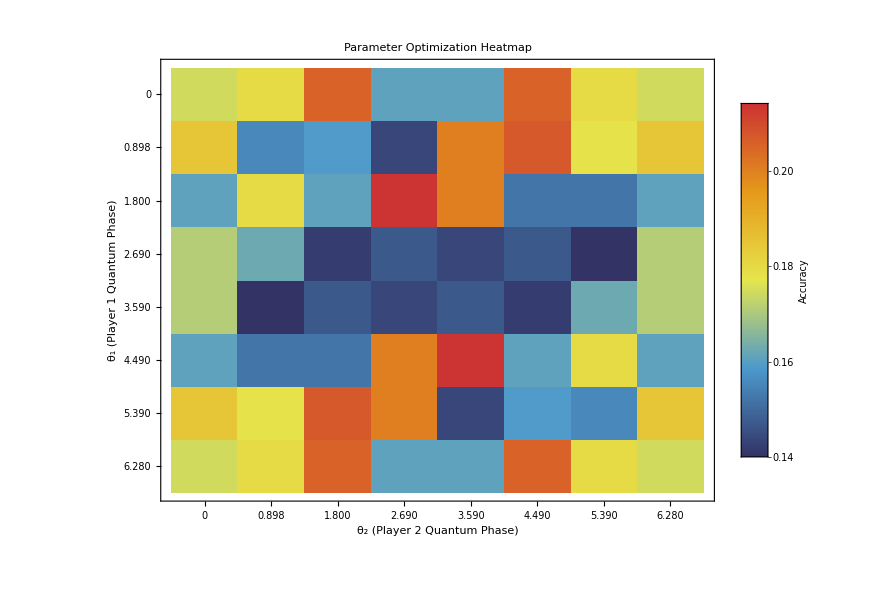

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
l1=1;
l2=1;
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=2.69279, θ2=1.7952, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.214162

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = 2.69279 θ2 = 1.7952 λ1 = 1 λ2 = 1 | Accuracy = 0.214162

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1
ACQ1 | 0 | 2 | 2 | 0 | 0 | 0 | 2
ACQ2 | 0 | 52 | 2 | 0 | 0 | 24 | 21
CAP1 | 0 | 18 | 6 | 0 | 0 | 12 | 20
CAP2 | 0 | 45 | 3 | 0 | 0 | 27 | 24
NEGO | 0 | 26 | 7 | 0 | 0 | 39 | 27
SQ | 0 | 27 | 4 | 0 | 0 | 41 | 27
WAR1 | 0 | 38 | 4 | 0 | 0 | 32 | 25

#### Setting 2: Lambda1 = 0.5 | Lambda2 = 0.5

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =0.5;
l2=0.5;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 64 parameter combinations...

Theta1 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Theta2 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Lambda1 = 0.5, Lambda2 = 0.5

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=0, Accuracy=0.17962

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Progress: 3/64 (4.69%)

Elapsed: 1.1 min, Estimated remaining: 23. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(6 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(8 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 6/64 (9.38%)

Elapsed: 3.1 min, Estimated remaining: 30. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(10 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(12 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 9/64 (14.1%)

Elapsed: 5.2 min, Estimated remaining: 31. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 12/64 (18.8%)

Elapsed: 7.1 min, Estimated remaining: 31. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(6 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(8 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(10 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 15/64 (23.4%)

Elapsed: 9.4 min, Estimated remaining: 31. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(12 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(4 π)/7, θ2=0, Accuracy=0.200345

Progress: 18/64 (28.1%)

Elapsed: 11. min, Estimated remaining: 29. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

```mathematica
analyzeCurrentResults[gridResults]
```

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.214162

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

#### Setting 3: Lambda1 = 2 | Lambda2 = 2

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =2;
l2=2;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

```mathematica
analyzeCurrentResults[gridResults]
```

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.214162

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

#### Setting 4: Lambda1 = 0.1 | Lambda2 = 0.1

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =0.1;
l2=0.1;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

```mathematica
analyzeCurrentResults[gridResults]
```

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.214162

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

#### Setting 5: Lambda1 = 10 | Lambda2 = 10

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =10;
l2=10;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

```mathematica
analyzeCurrentResults[gridResults]
```

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.214162

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```